# Test Pixel Alignment in Y - Axis (Inverted?)

```mathematica
tempImageData=ImageData[-Graphics-];
```

```mathematica
Dimensions[tempImageData]
```

{72,72,3}

```mathematica
Do[
PrependTo[tempImageData, Table[{0,0,0}, {72}]],
{10}
]
```

```mathematica
Image[tempImageData]
```

-Graphics-

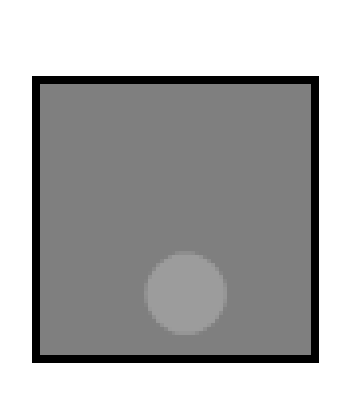

```mathematica
ArrayPlot[Map[Norm,tempImageData,{2}]]
```

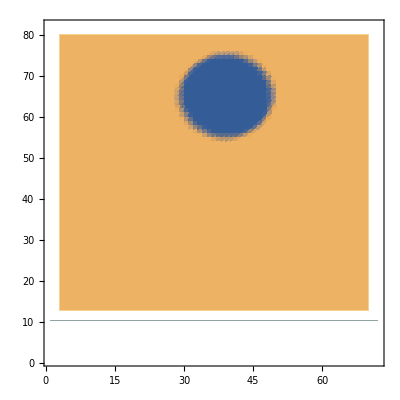

```mathematica
ListDensityPlot[Map[Norm,tempImageData,{2}]]
```